# ODE Integration

## Using Euler' s Method, which isn't very stable

## Setup

```mathematica
f[x_]:= -y[x];
```

```mathematica
y[0.0] = 1;
```

```mathematica
numSteps = 100;
```

## Integration Algorithm

```mathematica
h=N[1/numSteps];
```

```mathematica
euler[n_]:=y[(n-1)* h] + h * f[(n-1) * h]
```

```mathematica
Table[y[i * h] = euler[i],{i,1,numSteps}]
```

{0.99,0.9801,0.970299,0.960596,0.95099,0.94148,0.932065,0.922745,0.913517,0.904382,0.895338,0.886385,0.877521,0.868746,0.860058,0.851458,0.842943,0.834514,0.826169,0.817907,0.809728,0.801631,0.793614,0.785678,0.777821,0.770043,0.762343,0.754719,0.747172,0.7397,0.732303,0.72498,0.717731,0.710553,0.703448,0.696413,0.689449,0.682555,0.675729,0.668972,0.662282,0.655659,0.649103,0.642612,0.636185,0.629824,0.623525,0.61729,0.611117,0.605006,0.598956,0.592966,0.587037,0.581166,0.575355,0.569601,0.563905,0.558266,0.552683,0.547157,0.541685,0.536268,0.530906,0.525596,0.520341,0.515137,0.509986,0.504886,0.499837,0.494839,0.48989,0.484991,0.480141,0.47534,0.470587,0.465881,0.461222,0.45661,0.452044,0.447523,0.443048,0.438618,0.434231,0.429889,0.42559,0.421334,0.417121,0.41295,0.40882,0.404732,0.400685,0.396678,0.392711,0.388784,0.384896,0.381047,0.377237,0.373464,0.36973,0.366032}

## Error Analysis

### Derive Analytic Solution

```mathematica
analyticSolutionRule = DSolve[y'[x] == -y[x],y[x],x][[1]]
```

{y[x]→ⅇ^-x C[1]}

```mathematica
analyticSolutionRuleWithInitialValue = analyticSolutionRule /. {C[1] -> y[0]}
```

{y[x]→ⅇ^-x}

```mathematica
analyticSolution[x_]= (y[x] /. analyticSolutionRuleWithInitialValue);
```

### Plot Analytic Solution

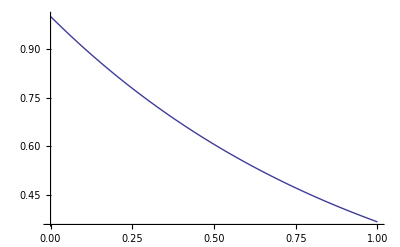

```mathematica
Plot[analyticSolution[x],{x,0,1}]
```

### Plot Approximate Solution

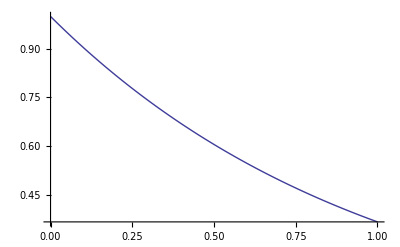

```mathematica
approximateSolution = Table[{h * i,y[h * i]},{i,0,numSteps}];
ListPlot[approximateSolution,Joined-> True]
```

### Plot Error

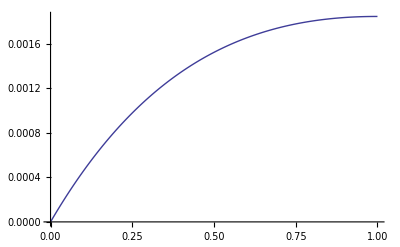

```mathematica
error = Table[{h * i,Abs[y[h * i] - analyticSolution[h * i]]},{i,0,numSteps}];
ListPlot[error,Joined-> True]
```